# AD Faked QN+ From Scratch

## Test Functions: “Rosen[a]”, “CRosen[a]”, “LIARWHD”, “ARWHEAD” [0] is objective, [1] is gradient, [2] is Hessian. Parameters get passed first!

#### Rosenbrock: “Rosen[a]”

```mathematica
Rosen[a_][0][x_List]:= Sum[a*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,{i, Length[x]-1}]
Rosen[a_][1][x_List]:= Module[{n=Length[x]},
Join[
{-2*(1-x⟦1⟧)-4*a *x⟦1⟧ (-x⟦1⟧^2+x⟦2⟧)},
Table[ -2*(1-x⟦i⟧)+2*a (-x⟦-1+i⟧^2+x⟦i⟧)-4*a x⟦i⟧ (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*a(x⟦n⟧-x⟦n-1⟧^2)}]
]
Rosen[a_][2][x_List]:=Module[{n=Length[x],MainDiagonal,OffDiagonal},
MainDiagonal=Join[
{2+8*a x⟦1⟧^2-4*a (-x⟦1⟧^2+x⟦2⟧)},
Table[2*a+2+8*a x⟦i⟧^2-4*a (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*a}];
OffDiagonal=-4*a*x⟦1;;n-1⟧;
SparseArray[{
Band[{1,2}]->OffDiagonal,
Band[{2,1}]->OffDiagonal,
Band[{1,1}]->MainDiagonal
},{n,n}]
]
```

#### Cuter Rose “CRosen[a]”

```mathematica
Clear[CRosen]
CRosen[a_][0][x_List]:= Module[{n=Length[x]},
1+Sum[a(x⟦i⟧-x⟦i-1⟧^2)^2,{i,2, n}]+Sum[(x⟦i⟧-1)^2,{i,2, n}]]
CRosen[a_][1][x_List]:= Module[{n=Length[x]},
Join[
{-4*a*x⟦1⟧ (-x⟦1⟧^2+x⟦2⟧)},
Table[ 2 (-1+x⟦i⟧)+2*a (-x⟦-1+i⟧^2+x⟦i⟧)-4*a x⟦i⟧ (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*(-1+x⟦n⟧)+2*a (-x⟦n-1⟧^2+x⟦n⟧)}]
]
CRosen[a_][2][x_List]:=Module[{n=Length[x],MainDiagonal,OffDiagonal},
MainDiagonal=Join[
{8*a*x⟦1⟧^2-4*a (-x⟦1⟧^2+x⟦2⟧)},
Table[2*a+2+8*a *x⟦i⟧^2-4*a (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*a+2}];
OffDiagonal=-4*a*x⟦1;;n-1⟧;
SparseArray[{
Band[{1,2}]->OffDiagonal,
Band[{2,1}]->OffDiagonal,
Band[{1,1}]->MainDiagonal
},{n,n}]
]
```

#### LIARWHD: “LIARWHD”

Implementing from Overleaf.

```mathematica
Clear[LIARWHD]
LIARWHD[0][x_List]:= Module[{n=Length[x]},
4*Sum[(x⟦i⟧^2-x⟦1⟧)^2,{i,1, n}]+Sum[(x⟦i⟧-1)^2,{i,1, n}]]
LIARWHD[1][x_List]:=Module[{n=Length[x]},
Join[ {-8*Sum[(x⟦i⟧^2-x⟦1⟧),{i,2,n}]+ 8*(x⟦1⟧^2-x⟦1⟧)(2*x⟦1⟧-1)+2*(x⟦1⟧-1)}, 
Table[ 2*(x⟦i⟧-1)+ 16 *x⟦i⟧ (x⟦i⟧^2-x⟦1⟧),{i,2,n}]]]
LIARWHD[2][x_List]:=Module[{n=Length[x]},
SparseArray[{
{1,1}-> (8n+2-48 x⟦1⟧+48 x⟦1⟧^2),
Band[{2,1},{n,1},{1,0}]-> -16*x⟦2;;n⟧,
Band[{1,2},{1,n},{0,1}]-> -16*x⟦2;;n⟧,
Band[{2,2}]-> Table[(2-16 x⟦1⟧+ 48 x⟦i⟧^2),{i,2,n}]
},{n,n}]]
```

#### ARWHEAD: “ARWHEAD”

Implementing from Overleaf with the parenthesis  in the last term.

```mathematica
Clear[ARWHEAD]
ARWHEAD[0][x_List]:=Module[{n=Length[x]},
 Sum[(x⟦i⟧^2+x⟦n⟧^2)^2+(1-x⟦i⟧)^2,{i, n}]+ Sum[(-4*x⟦i⟧+3),{i, n-1}]
]
ARWHEAD[1][x_List]:=Module[{n=Length[x]},
Join[Table[-4-2*(1-x⟦i⟧)+4*x⟦i⟧(x⟦i⟧^2+x⟦n⟧^2),{i,1,n-1}],
{-2*(1-x⟦n⟧)+16 x⟦n⟧^3+ 4*x⟦n⟧*Sum[x⟦i⟧^2+x⟦n⟧^2,{i,1,n-1}]}]
]
ARWHEAD[2][x_List]:=Module[{n=Length[x]},
SparseArray[{
Band[{n,1},{n,n-1},{0,1}]->Table[8*x⟦i⟧x⟦n⟧,{i,1,n-1}],
Band[{1,n},{n-1,n},{1,0}]->Table[8*x⟦i⟧x⟦n⟧,{i,1,n-1}],
Band[{1,1}]->Table[2+8*x⟦i⟧^2+4*(x⟦i⟧^2+x⟦n⟧^2),{i,1,n-1}],
{n,n}-> 2+16*3*x⟦n⟧^2+4*Sum[(x⟦i⟧^2+x⟦n⟧^2),{i,1,n-1}]+ 8*(n-1)*x⟦n⟧^2},{n,n}]
]
```

#### GENHUMPS: “GENHUMPS”

Implementing from Overleaf with the parenthesis  in the last term.

```mathematica
Clear[GENHUMPS]
GENHUMPS[0][x_List]:=Module[{n=Length[x]},
 Sum[(Sin[2x⟦i⟧] Sin[2 x⟦i+1⟧])^2+0.05 (x⟦i⟧^2+x⟦i+1⟧)^2,{i, n-1}]
]
GENHUMPS[1][x_List]:=Module[{n=Length[x]},
Join[
{0.2x⟦1⟧ (x⟦1⟧^2+x⟦2⟧)+4 Cos[2 x⟦1⟧] Sin[2 x⟦1⟧] Sin[2 x⟦2⟧]^2},
Table[0.1 (x⟦i-1⟧^2+x⟦i⟧)+0.2 x⟦i⟧ (x⟦i⟧^2+x⟦i+1⟧)
+4 Cos[2 x⟦i⟧] Sin[2 x⟦i-1⟧]^2 Sin[2 x⟦i⟧]+4 Cos[2 x⟦i⟧] Sin[2x⟦i⟧] Sin[2 x⟦i+1⟧]^2,{i,2,n-1}],
{0.1*(x⟦n-1⟧^2+x⟦n⟧)+4 Cos[2 x⟦n⟧] Sin[2 x⟦n-1⟧]^2 Sin[2 x⟦n⟧]}]
]
GENHUMPS[2][x_List]:=Module[{n=Length[x],OffDia},
OffDia=Table[0.2 x⟦i⟧+16 Cos[2 x⟦i⟧] Cos[2 x⟦i+1⟧] Sin[2 x⟦i⟧] Sin[2 x⟦i+1⟧],{i,1,n-1}]; 
SparseArray[{
{1,1}->0.4 x⟦1⟧^2+0.2 (x⟦1⟧^2+x⟦2⟧)+8 Cos[2 x⟦1⟧]^2 Sin[2 x⟦2⟧]^2-8 Sin[2 x⟦1⟧]^2 Sin[2 x⟦2⟧]^2,
Band[{2,2}]->Table[0.1-4 Cos[2 x⟦i⟧]^2 (-2+Cos[4 x⟦-1+i⟧]+Cos[4 x⟦1+i⟧])+0.6 x⟦i⟧^2+0.2 x⟦1+i⟧-8 Sin[2 x⟦-1+i⟧]^2 Sin[2 x⟦i⟧]^2-8 Sin[2 x⟦i⟧]^2 Sin[2 x⟦1+i⟧]^2,{i,2,n-1}],
{n,n}->0.1+8 Cos[2 x⟦n⟧]^2 Sin[2 x⟦n-1⟧]^2-8 Sin[2 x⟦n-1⟧]^2 Sin[2 x⟦n⟧]^2,
Band[{2,1}]->OffDia,
Band[{1,2}]->OffDia},{n,n}]
]
```

```mathematica
n=6;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
Simplify[Chop[D[GENHUMPS[0][vars],{vars,2}]-GENHUMPS[2][vars]]]//Chop
D[GENHUMPS[0][vars],{vars,1}]-GENHUMPS[1][vars]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{0.,0.,0.,0.,0.,0.}

### Derivative Tests

Testing the derivative formulas

```mathematica
a=23.0;
TestFnList={Rosen[a],CRosen[a], LIARWHD,ARWHEAD,GENHUMPS};
n=15;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
x0=RandomReal[{-1,1},n];
varsSub=Table[vars⟦i⟧->x0⟦i⟧,{i,n}];
{Max[Abs[
Chop[
Table[f[1][x0]-D[f[0][vars],{vars}]/.varsSub,{f,TestFnList}]
]]],
Max[Abs[
Chop[
Table[f[2][x0]-D[f[0][vars],{vars,2}]/.varsSub,{f,TestFnList}]
]]]}
```

{0,0}

### Critical Points and Characterizations

#### Duplicate Global Minima

The first observation is that CRosen has duplicate double global minima of 0 at
	(±1,1,1,1,…,1)

```mathematica
n=10;
xp=xm=ConstantArray[1,n];xm⟦1⟧=-1;
Map[Rosen,{xp,xm}]
Map[CRosen,{xp,xm}]
```

#### CP search

To keep this speedy I am not making it take more steps. First an assessment of the easiness of finding CPs,  I am going to run FindRoot out of the box and on the same ICs see how often it succeeds in finding a CP.  Finding CPs is way easier with the CUTER Rosenbrock!

```mathematica
n=6; 
Samples=123;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

```mathematica
n=12; 
Samples=123;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

```mathematica
n=32; 
Samples=123;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

```mathematica
n=52; 
Samples=223;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

#### CP Classification search

The plan now is to automate the search for as many types of CPs as I can find for CRosen.  I know the CP structure for Rosenbrock.  So I am focusing on the variant. I can probably do the computation up to n=7 or 8.  All the way up to 7 there are the two matched global minima and a single saddle.

```mathematica
n=4;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=N[vars/.Solve[ dRosen[vars]==0.0,vars, Reals]];
TableForm[
Map[Eigenvalues[ddRosen[#]]&,CPs],
TableHeadings->Automatic]
```

```mathematica
n=7;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=N[vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]];
TableForm[
Map[Eigenvalues[ddCRosen[#]]&,CPs],
TableHeadings->Automatic]
```

The single saddle is at {,…,} and the single negative eigenvalue looks to always be the same value of

There is a saddle in 2 dimensions. separating the two minima.

```mathematica
n=2;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]
```

The first non-trivial value for the saddle is the root of a cubic for n=3!

```mathematica
n=3;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]
Normal[CPs⟦2,2,1⟧][x]
```

```mathematica
n=4;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]
Normal[CPs⟦2,2,1⟧][x]
N[CPs]
```

#### Pics

The do not even look alike for n=2;

```mathematica
TabView[{
"Rosen"->ContourPlot[ Rosen[{x1,x2}], {x1,-1.8,1.8},{x2,-1.2,1.2},
PlotPoints->20,
PlotRange->{0,10},
Contours->30],
"CRosen"->ContourPlot[CRosen[{x1,x2}], {x1,-1.8,1.8},{x2,-1.2,1.2},
PlotPoints->20,
PlotRange->{0,10},
Contours->30]}]
```

I do not think that there is going to be any interesting CPs for the CRosen.  If there are they are hard to find.

I will try to do this a bit later.

## Code

### UnderFlow happens when the radius got too small. I added a kill switch to the loop control.

In older versions of Mma you could set an option to not catch underflows. This has vanished.  I left the call here in case it comes back.

```mathematica
SetOptions[MatrixPlot, PlotLegends->Automatic, AspectRatio->1];
SetSystemOptions["CatchMachineUnderflow"->False]
```

SetSystemOptions::sysname: CatchMachineUnderflow is not a known SystemOption.

SetSystemOptions[CatchMachineUnderflow→False]

### Orthogonalization and Random Generators

```mathematica
Orth[A_]:=Transpose[Orthogonalize[Transpose[A]]]
RandOrth[{m_,n_}]:= If[n>0,Orth[RandomReal[{-1,1},{m,n}]],{}]
RandSym[λs_]:= Module[{m=Length[λs],Q},
Q=RandOrth[{m,m}];
Q.DiagonalMatrix[λs].Qᵀ]
```

To make a random SPD specify positive eigenvalues.

```mathematica
dist=MixtureDistribution[{0.25,0.75},{NormalDistribution[2,1],NormalDistribution[10,1]}];
λs=Sort[RandomVariate[dist,m]];
A= RandSym[λs];
Norm[λs-Sort[Eigenvalues[A]]]
```

### QN Updates

```mathematica
bSR1[H_,U_,V_,δ_]:= Module[{UMinusHV=U-H.V,Temp},
Temp=H+ UMinusHV.PseudoInverse[UMinusHVᵀ.V,Tolerance->δ].UMinusHVᵀ;
(* in exact arithmetic or with a Sym tag this is not needed *)
0.5(Temp+Tempᵀ)
]
bPSB[H_,U_,V_,δ_]:= Module[{T1=PseudoInverse[Vᵀ.V,Tolerance->δ], T2, Temp},
T2=V.T1.(U-H.V)ᵀ;
Temp = H+T2 + T2ᵀ-T2.V.T1.Vᵀ;
(* in exact arithmetic or with a Sym tag this is not needed *)
0.5(Temp+Tempᵀ)
]

HUpdate[HTag_][HApprox_,{U_,V_},{p_,Newg_,gVal_},δ_]:= Module[{Delg=Newg-gVal,NewH},
(* I have two different updates switched with the HTag *)
(* The colorado papers say "Do the secant update" *)
(* I need to do it before I do the blocksample update *)
(* to maintain "exact" on search directions.  *)
Switch[HTag,
"SR1 with Secant",NewH=bSR1[HApprox,{p}ᵀ,{Delg}ᵀ,δ];NewH= bSR1[NewH,U,V,δ],
"PSB with Secant",NewH=bPSB[HApprox,{p}ᵀ,{Delg}ᵀ,δ];NewH= bPSB[NewH,U,V,δ],
"SR1 without Secant",NewH= bSR1[HApprox,U,V,δ],
"PSB without Secant",NewH= bPSB[HApprox,U,V,δ],
_,         Print["Update: HTag error!"];Abort[]]  ;
NewH
]
HTagList={"SR1 with Secant","PSB with Secant","SR1 without Secant","PSB without Secant"};
```

Testing on little guys.  The updates work fine with non-orthogonal inputs U. We are orthogonalizing for convenience and because it seems like the right thing to do.  Without the explicit symmetrization the PSB update is way more symmetric than the SR1.

```mathematica
{n,w,δ}={231,16,1.0*10^-6};
dist=MixtureDistribution[{0.5,0.5},{NormalDistribution[-2,1],NormalDistribution[2,1]}];
λs=Sort[RandomVariate[dist,n]];
A= RandSym[λs]; 
H=RandSym[RandomReal[{-1,1},n]];
U=RandomReal[{-1,1},{n,w}];V=A.U;
{Hs,Hp}=Map[#[H,U,V,δ]&,{bSR1,bPSB}];
(* Test for Symmetry *)
Map[Norm[#-#ᵀ]&,{Hs,Hp}]
(* Test Secant Condition *)
Map[Norm[#.V-U]&,{Hs,Hp}]
```

### gHS

The plan is to fake the AD update in the paper Alg4.1.  Since I am faking AD it needs  df and ddf.  I am matching the output format for clarity.

```mathematica
gHSFake[f_][{x_,S_}]:= Module[{g=f[1][x],J=f[2][x],Y},
Y = J.S;
{g, J.g, Y}]
(* Overload for NO samples *)
gHSFake[f_][{x_,{}}]:= Module[{g=f[1][x],J=f[2][x]},
{g, J.g,{}}]
```

Testing a bit.  OK one of the thing to realize is that I made S unit sized so Y is average eigenvalue sized.  However, the gradient g could well be very large or very small with correspondingly sized output h=J.g.  I do not want to mess with gHS but I am going to scale this portion of the input to the QN update.

```mathematica
a=100;
{n,w}={37,4};
x0=RandomReal[{-1,1},n];
S=RandOrth[{n,2*w-1}];
{g,h,Y}=gHSFake[Rosen[a]][{x0,S}];
Sg = ArrayFlatten[{{S,{g}ᵀ}}];
Yh = ArrayFlatten[{{Y,{h}ᵀ}}];
J = Rosen[a][2][x0];
TabView[{
"S"->MatrixPlot[S],
"Y"->MatrixPlot[Y],
"J.S" ->MatrixPlot[J.S],
"Sg"->MatrixPlot[Sg],
"Yh"->MatrixPlot[Yh],
"J.Sg" ->MatrixPlot[J.Sg]}]
```

123456

### NEW: Initializing H using Hessian Samples

The Hessian sample Y_0=∇^2 f(x_0)S_0 with S_0 provides a conservative and consistent estimate for H_0.  Remember H^-1≈∇^2 f(x).  Estimate is α Id.

```mathematica
αFromgHS[{g_,h_,Y_},S_]:= Module[ {λs,α},
λs =Eigenvalues[Sᵀ.Y] ;  (* SᵀY=Sᵀ∇^2 f(Subscript[x, 0])S and S is orthogonal *)
(* H0 estimate is α Id *)
(* It would also be consistent to use *)
(* α = 1/Mean[λs]; I do not have a preference and do not expect any difference in performance *)
α = 0.5*(Mean[1/λs]+1/g.h)
]
(* Overload for no samples use the*)
αFromgHS[{g_,h_,{}},{}]:=1/g.h
```

### U,V input for QN from gHS output

The output from gHS  is {g,h,Y} from input {x,S} where g=∇f(x), h=∇^2 f(x).g, and Y=∇^2 f(x).S.  I am orthogonalizing S so Y gives eigenvalue estimates.  However g is not normalized.  Before I put this into the QN update I am going to normalize g.

```mathematica
BuildUVFromgHSOutput[{g_,h_,Y_},S_]:= Module[{gNorm =Norm[g]},
{ArrayFlatten[{{S,{g}ᵀ/gNorm}}],ArrayFlatten[{{Y,{h}ᵀ/gNorm}}]}] 
(* Overload for no samples *)
BuildUVFromgHSOutput[{g_,h_,{}},{}]:= Module[{gNorm =Norm[g]},
{{g}ᵀ/gNorm,{h}ᵀ/gNorm} ]
```

```mathematica
{n,w}={37,4};
x0=RandomReal[{-1,1},n];
S=RandOrth[{n,2*w-1}];
a=100;
{g,h,Y}=gHSFake[Rosen[a]][{x0,S}];
{U,V}=BuildUVFromgHSOutput[{g,h,Y},S];
J = Rosen[a][2][x0];
Norm[V-J.U,"Frobenius"]
TabView[{
"U"->MatrixPlot[U],
"V"->MatrixPlot[V],
"J.U" ->MatrixPlot[J.U]}]
```

2.36197×10^-13

123

### TRS

Direct implementation of the GEV trust region sub solve using the  algorithm from 
“Solving the Trust Region Sub Problem by a Generalized Eigenvalue Problem”
S. Adachi, S. Iwata, Y. Nakatsukasa, and A. Takeda.    SIAM 2017

Use their notation etc. minimizes 
	0.5 p.A.p+g.p
for 
	p.B.p≤Δ^2
Where A and B are sym. B is SPD and Δ (the trust region radius) is positive.  The underlying dimension is n.  I am mimicking the input and output formats of the Julia TRS implementation from https://github.com/oxfordcontrol/TRS.jl
	(p,info)←trs(A,q,Δ,B;kwargs)
The arguments do not have the same names: A↔P, B↔C.  The main body of our algorithm aligns with the TRS usage because it was less confusing for Dan.  I am not doing the info and keyword args right now.  The algorithm is pretty simple.  It is just one of the standard linearizations of the QEP that you get when you write the Lagrange multiplier form.

```mathematica
TRS[A_,g_,Δ_,B_]:= Module[{n=Length[A],CP,M0,M1,λs,vs,
GapIndex,MaxIndex,λMax,vMax,gap,τ,y1,y2},
(* Compute Critical point *)
Check[CP = LinearSolve[A,-g],(*TRSDump={A,g,Δ,B};*) Abort[]];
If[  
(* Test if CP is internal and CP is a min i.e. A is SPD. *)
 And[CP.B.CP ≤Δ^2, Min[Eigenvalues[A]]≥0],CP,
(* return interior min if appropriate otherwise *)
(* Doing the smaller matrix pencil 3.2 *)
{M0,M1} = Map[ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),-({{0, B}, {B, 0}})}];
(* compute all GEV pairs M0.v = λ M1.v *)
(* compute GEV pair associated with largest (most positive) eigenvalue *)
{λs,vs}=Check[Eigensystem[{M0,M1}],Dump={{M0,M1},{A,g,Δ,B}};Abort[]];
(* Find and return most positive eigenvalue eigenvector pair *)
{GapIndex,MaxIndex}=Ordering[Re[λs],-2];
{λMax,vMax}={λs⟦MaxIndex⟧,vs⟦MaxIndex⟧};
(* Compute gap *)
gap = Abs[λMax-λs⟦GapIndex⟧];
τ=10^-8*gap^-0.5;
(* Split the eigenvector *)
(* Max evec is real so trash 0.0 I *)
{y1,y2}=Re[{vMax⟦1;;n⟧,vMax⟦n+1;;2n⟧}];
If[(*Print[{Norm[y1],τ}]; *)Norm[y1]>τ,
(* Test for hard case. If not return easy version *)
N[-Sign[g.y2] (Δ y1)/(√(y1.B.y1))],
(* Hard version to come right now just flagged *)
Print["TRS: HardCase not implemented!"];ConstantArray[0,n]]
]
]
```

Test.  Code works but hard case output is not implemented.   Throws a printed warning and returns the zero vector if it ever hits the hard case.   It does not hit a hard case on randomized input.  The TRS algorithm gives better constraint satisfaction (always floating point satisfied) and lower objective values!

```mathematica
Clear[p,pvars]
m=123;
A=RandSym[RandomReal[{-12,20},m]];
g=RandomReal[{-1,1},m];
B= RandSym[RandomReal[{0.1,1},m]];
Δ=RandomReal[{0.000001,10}];
p0=RandomReal[{-1,1},m];
pvars=Table[Symbol[StringJoin["$p",ToString[i]]],{i,m}];
{FMmin,FMSub}=FindMinimum[ {0.5 pvars.A.pvars + g.pvars,pvars.B.pvars≤Δ^2},{pvars,p0}ᵀ] ;
TRSSub =  {p-> TRS[A,g,Δ,B]};
TableForm[
{
{√(p.B.p),Δ-√(p.B.p),Δ≥√(p.B.p),(0.5 p.A.p + g.p) }/.TRSSub, 
{√(pvars.B.pvars),Δ-√(pvars.B.pvars),Δ≥√(pvars.B.pvars),(0.5 pvars.A.pvars + g.pvars) }/.FMSub
},
TableHeadings->{{"TRS","FindMin"},
{"Cons","Cons-Gap","Cons T/F","Objective-Low is better"}}
]
```

| Cons | Cons-Gap | Cons T/F | Objective-Low is better
TRS | 8.25841 | 0. | True | -1111.04
FindMin | 8.25841 | -2.67049×10^-10 | False | -1111.04

#### Dan’s Hard Case Data

Dan shared some data on Sept 24 from his code which triggered the “funny” trs behavior.  
I copied and parse it to see if I can work out what is going on.

```mathematica
b={4.196556681368875*10^-12,-2.2110729634504618*10^-13,1.2009342726705275*10^-9,3.831614385134228*10^-10,-1.1110777656755573*10^-9};
P={
{3.429819497176883*10^-9,4.196556681368876*10^-12,7.095187975775695*10^-7,1.9801872464854584*10^-7,-3.495742483146149 *10^-7},
{4.196556681368876*10^-12,-2.2110729634504626*10^-13, 1.2009342726203648*10^-9, 3.8316143850221347*10^-10,-1.111077765637876*10^-9},
{7.095187975775695*10^-7,1.2009342726203648*10^-9,574.6946694141305,4.864307678200925,0.23648172978120385},
{1.9801872464854584*10^-7,3.8316143850221347*10^-10,4.864307678200925,488.798776681566,0.12290792553140761},
{-3.495742483146149*10^-7,-1.111077765637876*10^-9, 0.23648172978120385, 0.12290792553140761, 285.11808213394914}};
CMat={
{4.1965566813001324*10^-12,-2.211072962897013*10^-13, 1.2009342665066224*10^-9, 3.8316146143946595*10^-10,-1.1110777705468554*10^-9},
{-2.211072962897013*10^-13,3.7989868152082155*10^-13,-7.189364208030209*10^-10, 1.0098068115159453*10^-9,-3.26596532573809*10^-10},
{1.2009342665066224*10^-9,-7.189364208030209*10^-10, 1.0000000000000084, 5.5246145975737165*10^-12,-9.698908343125368*10^-13},
{3.8316146143946595*10^-10, 1.0098068115159453*10^-9, 5.5246145975737165*10^-12, 0.9999999999947149,-1.7621459846850485*10^-12},
{-1.1110777705468554*10^-9,-3.26596532573809*10^-10,-9.698908343125368*10^-13,-1.7621459846850485*10^-12, 1.0000000000004219}};
TableForm[Map[Eigenvalues,{P,CMat}],
TableHeadings->{{"P","CMat"},Automatic}]
Map[NullSpace[#,Tolerance->10^(-10)]&,{P,CMat}]
```

```mathematica
Δ=0.01;
TRS[P,b,Δ,CMat]
```

### Builds for quadratic models and TRS args

Building out the formula chain from section 6.  I modified this to use the scaled gradient and h fro the explicit representation Q for the search space.

```mathematica
SubProblemSolve[H_,g_,S_,Y_,Δ_]:= Module[
{h=H.g, Q,P,b,CMat,gNorm=Norm[g]},
(* SubProbDump={H,g,Y,S};*)
(* CMat to avoid MMa namespace collision *) 
(* space Representation 6.5 *)
(*The scaled and orthogonalized verion produces better conditioned matrices *)
Q=Orth[ArrayFlatten[ {{{h}ᵀ/gNorm,{g}ᵀ/gNorm,Y}}]];
(*Q=ArrayFlatten[ {{{h}ᵀ,{g}ᵀ,Y}}];*)
(* Args for trs solver 6.9  *)
P=Qᵀ.H.Q; b=Qᵀ.H.g; CMat=Qᵀ.H.H.Q;
(* resolving the namespace conflicts with TRS P↔A, b↔g, Δ↔Δ, CMat↔B *)
(* TRS call is TRS[A, g, Δ,B] *)
(* TRS call flags but does not solve the HardCase *)
(*SubProblemSolveDump={Q,P,b,Δ,CMat,"not empty"};*)
Q.TRS[P,b,Δ,CMat]
(* returns the q update. p=H.q is the p update x-> x+p = x + H.q *)
]
(* Overload for NO samples *) 
SubProblemSolve[H_,g_,{},{},Δ_]:= Module[
{h=H.g, Q,P,b,CMat,gNorm=Norm[g]},
(* CMat to avoid MMa namespace collision *) 
(* space Representation 6.5 *)
(*The scaled and orthogonalized verion produces better conditioned matrices *)
Q=Orth[ArrayFlatten[ {{{h}ᵀ/gNorm,{g}ᵀ/gNorm}}]];
(*Q=ArrayFlatten[ {{{h}ᵀ,{g}ᵀ,Y}}];*)
(* Args for trs solver 6.9  *)
P=Qᵀ.H.Q; b=Qᵀ.H.g; CMat=Qᵀ.H.H.Q;
(* resolving the namespace conflicts with TRS P↔A, b↔g, Δ↔Δ, CMat↔B *)
(* TRS call is TRS[A, g, Δ,B] *)
(* TRS call flags but does not solve the HardCase *)
(*SubProblemSolveDump={Q,P,b,Δ,CMat,"empty"};*)
Q.TRS[P,b,Δ,CMat]
(* returns the q update. p=H.q is the p update x-> x+p = x + H.q *)
]

pSubProblemBuild[InvH_,g_][p_]:=0.5 p.InvH.p+g.p
qSubProblemBuild[H_,g_][q_]:=0.5 q.H.q+(H.g).q
```

Testing some pieces together for an initial step on  the Rosenbrock function.  It looks pretty stable I have run it several times all but once SR1 and PSB have been close with PSB a smidge better on the objective. I have seen one failed step with SR1 and non with PSB.  The descent ration seems pretty consistently better than one! Except for the single SR1 failed step!

The first thing I do is check the two variant sub problem builds are equivalent.

First the version with S and Y non-empty.

```mathematica
{n,w,δ}={90,3,1.0*10^-10};
ΔMax=100;
x0=RandomReal[{-1.2,1.2},n];
S0=RandOrth[{n,2w-1}];
a=20;
f=Rosen[a];
{g0,h0,Y0}=gHSFake[f][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[{g0,h0,Y0},S0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* SR1 and PSB Udates *)
Hp = bPSB[H0,U0,V0,δ];
Hs = bSR1[H0,U0,V0,δ];
(* Compute  accurate Hessian and sanity check for updates! AD-CHEAT *) 
J0=f[2][x0];
TabView[{"J0^-1"->MatrixPlot[Inverse[J0]],
"Hs"->MatrixPlot[Hs],"Hp"->MatrixPlot[Hp],
"H0"->MatrixPlot[H0],"Hs-Hp"->MatrixPlot[Hs-Hp]}];
(* Initialize Step Size with min for 0.5 t^2/α0 + ||∇f||t i.e t=α||∇f||=α||g0||. Dan has "0.1||g0||" *)
(* I am scaling up by γ=1.1 so the Trust Region includes the 1D min. It is safegaurded but for now ΔMax is big at 100 *)
γ=1.1;
Δ=Min[γ*Norm[g0]*α0,ΔMax];
(* Sub problem steps *)
qs =SubProblemSolve[Hs,g0,S0,Y0,Δ]; ps=Hs.qs; 
qp =SubProblemSolve[Hp,g0,S0,Y0,Δ];  pp=Hp.qp;
(* Checking constraints and model values and function values *)
{Δ,Map[Norm,{ps,pp}]};
{Bs,Bp}=Map[Inverse,{Hs,Hp}];
TableForm[{
{Norm[ps], Norm[pp]},
{Δ-Norm[ps], Δ-Norm[pp]},
{0-qSubProblemBuild[Hs,g0][qs],0-qSubProblemBuild[Hp,g0][qp]},
{0-pSubProblemBuild[Bs,g0][ps],0-pSubProblemBuild[Bp,g0][pp]},
{f[0][x0]-f[0][x0+ps],f[0][x0]-f[0][x0+pp]},
{(f[0][x0]-f[0][x0+ps])/(0-pSubProblemBuild[Bs,g0][ps]),(f[0][x0]-f[0][x0+pp])/(0-pSubProblemBuild[Bp,g0][pp])},
{f[0][x0+ps],f[0][x0+pp]}
},
TableHeadings->{
{"||p||","Δ-||p||", "m[0]-m_q[q]","m[0]-m_p[p]","f[x]-f[x+p]","ρ", ToString[StringForm["f[x]=``→",f[0][x0]]]},
{"SR1","PSB"}}]
```

| SR1 | PSB
||p|| | 2.88909 | 2.74971
Δ-||p|| | 0.493877 | 0.633257
m[0]-m_q[q] | 1400.19 | 1401.83
m[0]-m_p[p] | 1400.19 | 1401.83
f[x]-f[x+p] | 1674.69 | 1693.81
ρ | 1.19604 | 1.20828
f[x]=2256.72→ | 582.031 | 562.913

Now with S=Y={}.

```mathematica
{n,w,δ}={90,1,1.0*10^-10};
ΔMax=100;
x0=RandomReal[{-1.2,1.2},n];
S0=RandOrth[{n,2w-1}];
a=20;
f=Rosen[a];
{g0,h0,Y0}=gHSFake[f][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[{g0,h0,Y0},S0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* SR1 and PSB Udates *)
Hp = bPSB[H0,U0,V0,δ];
Hs = bSR1[H0,U0,V0,δ];
(* Compute  accurate Hessian and sanity check for updates! AD-CHEAT *) 
J0=f[2][x0];
TabView[{"J0^-1"->MatrixPlot[Inverse[J0]],
"Hs"->MatrixPlot[Hs],"Hp"->MatrixPlot[Hp],
"H0"->MatrixPlot[H0],"Hs-Hp"->MatrixPlot[Hs-Hp]}];
(* Initialize Step Size with min for 0.5 t^2/α0 + ||∇f||t i.e t=α||∇f||=α||g0||. Dan has "0.1||g0||" *)
(* I am scaling up by γ=1.1 so the Trust Region includes the 1D min. It is safegaurded but for now ΔMax is big at 100 *)
γ=1.1;
Δ=Min[γ*Norm[g0]*α0,ΔMax];
(* Sub problem steps *)
qs =SubProblemSolve[Hs,g0,S0,Y0,Δ]; ps=Hs.qs; 
qp =SubProblemSolve[Hp,g0,S0,Y0,Δ];  pp=Hp.qp;
(* Checking constraints and model values and function values *)
{Δ,Map[Norm,{ps,pp}]};
{Bs,Bp}=Map[Inverse,{Hs,Hp}];
TableForm[{
{Norm[ps], Norm[pp]},
{Δ-Norm[ps], Δ-Norm[pp]},
{0-qSubProblemBuild[Hs,g0][qs],0-qSubProblemBuild[Hp,g0][qp]},
{0-pSubProblemBuild[Bs,g0][ps],0-pSubProblemBuild[Bp,g0][pp]},
{f[0][x0]-f[0][x0+ps],f[0][x0]-f[0][x0+pp]},
{(f[0][x0]-f[0][x0+ps])/(0-pSubProblemBuild[Bs,g0][ps]),(f[0][x0]-f[0][x0+pp])/(0-pSubProblemBuild[Bp,g0][pp])},
{f[0][x0+ps],f[0][x0+pp]}
},
TableHeadings->{
{"||p||","Δ-||p||", "m[0]-m_q[q]","m[0]-m_p[p]","f[x]-f[x+p]","ρ", ToString[StringForm["f[x]=``→",f[0][x0]]]},
{"SR1","PSB"}}]
```

| SR1 | PSB
||p|| | 2.54329 | 2.43556
Δ-||p|| | 0.328918 | 0.436647
m[0]-m_q[q] | 875.829 | 877.915
m[0]-m_p[p] | 875.829 | 877.915
f[x]-f[x+p] | 1051.67 | 1060.94
ρ | 1.20077 | 1.20848
f[x]=1448.58→ | 396.917 | 387.641

I am going to runs this a bunch of times and see what the ρs look like for both updates.  The data below takes a minute or so to generate.  It looks as though the first step is almost always successful. 
The bottom report is just summarizes the data.

```mathematica
{n,w,δ}={90,3,1.0*10^-10};
ΔMax=100; SampleSize=3000;
x0=RandomReal[{-1.2,1.2},n];
S0=RandOrth[{n,2w-1}];
a=20;
f=Rosen[a];
{ρsSR1,ρsPSB,ΔfsSR1,ΔfsPSB}=Table[
x0=RandomReal[{-1.2,1.2},n];
S0=RandOrth[{n,2w-1}];
{g0,h0,Y0}=gHSFake[f][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[{g0,h0,Y0},S0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* SR1 and PSB Udates *)
Hp = bPSB[H0,U0,V0,δ];
Hs = bSR1[H0,U0,V0,δ];
(* Initialize Step Size with min for 0.5 t^2/α0 + ||∇f||t i.e t=α||∇f||=α||g0||. Dan has "0.1||g0||" *)
(* I am scaling up by γ=1.1 so the Trust Region includes the 1D min. It is safegaurded but for now ΔMax is big at 100 *)
γ=1.1;
Δ=Min[γ*Norm[g0]*α0,ΔMax];
(* Sub problem steps *)
qs =SubProblemSolve[Hs,g0,S0,Y0,Δ]; ps=Hs.qs; 
qp =SubProblemSolve[Hp,g0,S0,Y0,Δ]; pp=Hp.qp;
(*  Descent Ratios *)
{Δ,Map[Norm,{ps,pp}]};
{(f[0][x0]-f[0][x0+ps])/(0-qSubProblemBuild[Hs,g0][qs]),(f[0][x0]-f[0][x0+pp])/(0-qSubProblemBuild[Hp,g0][qp]),(f[0][x0]-f[0][x0+ps])/(f[0][x0]),(f[0][x0]-f[0][x0+pp])/(f[0][x0])},
{SampleSize}]ᵀ;
TabView[{
"ρ"->PairedHistogram[Select[ρsSR1,(#>0)&],Select[ρsPSB,(#>0)&],
ChartLabels->{"ρSR1","ρPSB"}],
"Δf"->PairedHistogram[Select[ΔfsSR1,(#>0)&],Select[ΔfsPSB,(#>0)&],
ChartLabels->{"ΔfSR1","ΔfPSB"}]}
]
TableForm[Map[BinCounts[#,{{-∞,0,0.25,∞}}]&,{ρsSR1,ρsPSB}],
TableHeadings->{{"SR1","PSB"},{"Fail","Shrink","Good"}}]
```

12

| Fail | Shrink | Good
SR1 | 0 | 1 | 2999
PSB | 0 | 0 | 3000

My summary is that first steps are very reliable for both updates.  I have seen SR1 fail very occasionally.  I left one in the run above!

### Reduction Ratio

The reduction ratio is computed with the q model to reduce linear algebra.

```mathematica
Rho[fNew_,H_,g_,q_,fValIn_]:= (
(*Print[qSubProblemBuild[H,g][q]];*)
(fValIn-fNew)/(0-qSubProblemBuild[H,g][q])
)
```

### Sample Selection

We have three sample choices in the paper 6.1-6.3.  I trialed two others

```mathematica
SampleUpdate[STag_,ITag_][{S_,Y_,p_}]:= Module[
(* STag ∈ {"6.1","6.2","6.3"}, ITag ϵ {"With p_k","Without p_k"}  *)
{X=RandomVariate[NormalDistribution[0,1],Dimensions[S]]},
Switch[STag,
"6.1", X=X,      
"6.2", X=X-S.Sᵀ.X,
"6.3", X=Y-S.Sᵀ.Y,
(* Catch bad tags and abort computation *)
_,        Print["UpdateSample: STag error!"];Abort[]
];
If[ITag=="With p_k",X⟦All,-1⟧=p];
Orth[X]
];
STagITagList={{"6.1","6.2","6.3"},"With p_k"};
```

### QNStateInitialize

States are initialized with the H update specified by HTag.  This stores everything! The order is below.

```mathematica
Clear[QNStateInitialize]

QNStateInitialize[f_,HTag_,ΔMax_,δ_,w_][x0_]:= Module[
{n=Length[x0],S0,g0,h0,Y0,α0, H0,U0,V0,γ,Δ0,f0},
(* compute initial f value *)
f0=f[0][x0];
(* compute initial sample *)
If[w>0,S0=RandOrth[{n,2*w -1}],S0={}];
{g0,h0,Y0}=gHSFake[f][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[{g0,h0,Y0},S0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* Build first Hessian Update switched using HTag in HTagList *)
H0=Switch[StringTake[HTag,3],
"SR1",bSR1[H0,U0,V0,δ],
"PSB",bPSB[H0,U0,V0,δ],
_,         Print["Initial H Update: HTag error!"];Abort[]]  ;
(* Initialize Step Size **)
γ=1.1; Δ0=Min[γ*Norm[g0]*α0,ΔMax];
(* Return initialized state with ρ initialized to zero and NumGrads initialized to 1*)
{x0,f0,g0,h0,H0,Δ0,S0,Y0,0,1}
]
```

### QNUpdate including Trust region control

A step is accepted with appropriate updates if ρ≥0. The step is rejected if ρ<0 nothing is updated except the radius is backtracked Δ⟵0.25Δ. 
If the step is accepted the gradient is evaluated and the Hessian is sampled, approximate Hessian updated, and the radius is adjusted per 4.1. 
	0≤ρ<0.25  then  Δ⟵0.25Δ
	ρ≥0.75  and ||p||=Δ then  Δ⟵min(2 Δ,ΔMax)
Daniel made a nice Julia structure.  I am not doing that in Mathematica: this is verification not production!   My equivalent is just a list containing (the no longer minimal to enable easy plotting) state information for a QN iteration.  Hopefully the names below are self explanatory.  For those who do not do Mathematica the “control stuff out front” to make it easy to use the built-in iterators constructs.

The structure is 
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
"x" | "f" | "g=∇f" | "h=J.g" | "H" | "Rad" | "S" | "Y" | "ρ" | "#gHS"

```mathematica
Clear[QNUpdate]

QNUpdate[f_,STag_,HTag_,ITag_][{x_,fVal_,gVal_,JgVal_,HApprox_,Rad_,S_,Y_,ρ_,NumGrads_}]:= Module[
{δ=1.0*10^-12,MaxΔ=100,q,p,Newx,fNew,NewS,Newg,NewJg,NewY,U,V,NewH,NewRad,ρNew,λMax},
(*Print[i++];*)
(* Compute q using TRS *)
q=SubProblemSolve[HApprox,gVal,S,Y,Rad];
(* Build p from q and update x *)
p=HApprox.q; Newx=x+p;
fNew=f[0][Newx];
(* Compute ρ  *)
ρNew = Rho[fNew,HApprox,gVal,q,fVal];
(*Print[StringForm["ρ=``, fOld=`` > `` =fNew",ρNew,fVal,fNew]];*)
(* Update control *)
If[ fNew≥fVal, {x,fVal,gVal,JgVal,HApprox,0.25*Rad,S,Y,ρ,NumGrads}, (* reject step *)
(* Otherwise update S. Switched with tags in STagITagList *)
NewS=SampleUpdate[STag,ITag][{S,Y,p}];
(* update curvature info *)
{Newg,NewJg,NewY}=gHSFake[f][{Newx,NewS}];
(* Build U and V *)
{U,V}=BuildUVFromgHSOutput[{Newg,NewJg,NewY},NewS];
(* Update H switched with HTag in HTagList. Secant update first maintains "exact" on S.  *)
NewH=HUpdate[HTag][HApprox,{U,V},{p,Newg,gVal},δ];
(* Update radius *)
NewRad=Rad;
If[And[ρ>0.75,Norm[p]==Rad], NewRad = Min[2*Rad, MaxΔ]];
If[ρ<0.25, NewRad = 0.25*Rad];
(* Update everything *)
{Newx,fNew,Newg,NewJg,NewH,NewRad,NewS,NewY,ρNew,NumGrads+1}
]
]
```

Testing. Function choices are Rosen[a], CRosen[a], LIARWHD, or ARWHEAD or GENHUMPS.

## Test Pics

Tag choices are below.

```mathematica
HTagList
STagITagList
```

{SR1 with Secant,PSB with Secant,SR1 without Secant,PSB without Secant}

{{6.1,6.2,6.3},With p_k}

```mathematica
Clear[TabViewPic]
TabViewPic[STag_,HTag_,ITag_][QNData_]:= TabView[{
"||∇f||"->ListLogPlot[{QNData⟦All,-1⟧,Map[Norm,QNData⟦All,3⟧]}ᵀ, 
AxesLabel->{"#gHS","||∇f||"},PlotLabel->StringJoin[STag," ",HTag," ",ITag]],
"f"->ListLogPlot[{QNData⟦All,-1⟧,QNData⟦All,2⟧}ᵀ, 
AxesLabel->{"#gHS","∇f"},PlotLabel->StringJoin[STag," ",HTag," ",ITag]],
"rad"->ListLogPlot[{QNData⟦All,-1⟧,QNData⟦All,6⟧}ᵀ, 
AxesLabel->{"#gHS","Rad"},PlotLabel->StringJoin[STag," ",HTag," ",ITag]],
"ρ"->ListLogPlot[{QNData⟦All,-1⟧,QNData⟦All,-2⟧}ᵀ, 
AxesLabel->{"#gHS","ρ"},PlotLabel->StringJoin[STag," ",HTag," ",ITag]]}]
```

```mathematica
Clear[CompareObjectivePics]
CompareObjectivePics[LabelList_List,Title_][QNDataList_List]:= Module[{},
ListLogPlot[ 
Table[{QNDataList⟦i,All,-1⟧,QNDataList⟦i,All,2⟧}ᵀ
,{i, Length[QNDataList]}],
PlotLegends->LabelList, 
Joined->True,
AxesLabel->{"#gHS","∇f"},PlotLabel->Title]
]
```

1234

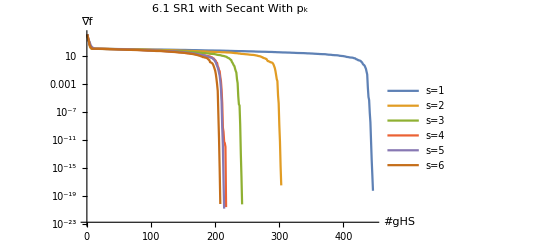

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag,HTag,ITag}={"6.1","SR1 with Secant","With p_k"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
QNDataList=Table[
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{w,1,6}];

i=4;
TabViewPic[STag,HTag,ITag][QNDataList⟦i⟧]
CompareObjectivePics[
Table[StringForm["s=``",i],{i,6}],StringJoin[STag," ",HTag," ",ITag]][QNDataList]
```

# Pics

## PSB Block Size

### Comparing Block Size for SR1 on std Rosen

Conclusion PSB is NOT competitive.  Not I had to increase the maximum number of iterations! Do not run again!

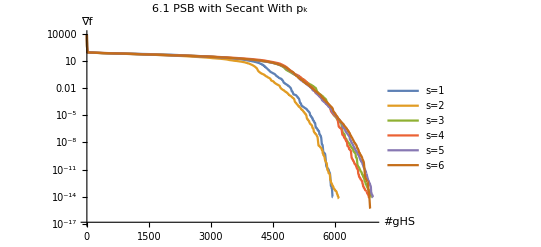

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag,HTag,ITag}={"6.1","PSB with Secant","With p_k"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^4,10^-12};
Clear[QNDataList]
QNDataList=Table[
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{w,1,6}];
CompareObjectivePics[
Table[StringForm["s=``",i],{i,6}],StringJoin[STag," ",HTag," ",ITag]][QNDataList]
```

```mathematica
TabView[Table[
w->TabViewPic[STag,HTag,ITag][QNDataList⟦w⟧],
{w,6}]]
```

123456

## SR1 Block Size variants

### Comparing Block Size for SR1 on std Rosen with Secant

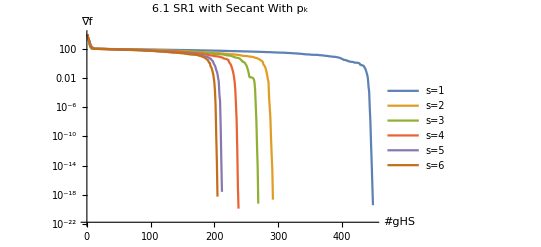

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag,HTag,ITag}={"6.1","SR1 with Secant","With p_k"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
QNDataList=Table[
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{w,1,6}];
CompareObjectivePics[
Table[StringForm["s=``",i],{i,6}],StringJoin[STag," ",HTag," ",ITag]][QNDataList]
```

### Comparing Block Size for SR1 on std Rosen without secant

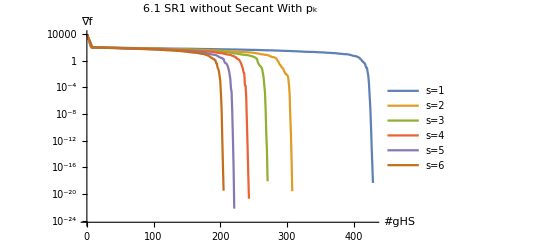

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag,HTag,ITag}={"6.1","SR1 without Secant","With p_k"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
QNDataList=Table[
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{w,1,6}];
CompareObjectivePics[
Table[StringForm["s=``",i],{i,6}],StringJoin[STag," ",HTag," ",ITag]][QNDataList]
```

### Comparing Block Size for SR1 on std Rosen without secant and without pk

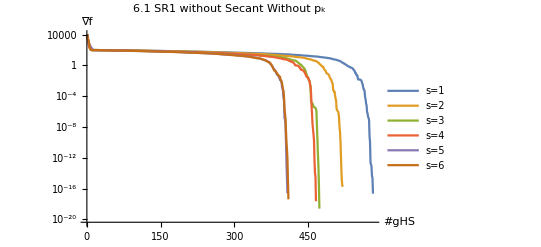

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag,HTag,ITag}={"6.1","SR1 without Secant","Without p_k"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
QNDataList=Table[
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{w,1,6}];
CompareObjectivePics[
Table[StringForm["s=``",i],{i,6}],StringJoin[STag," ",HTag," ",ITag]][QNDataList]
```

### Comparing Block Size for SR1 on std Rosen with secant and without pk

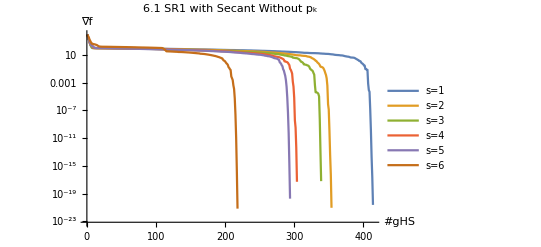

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag,HTag,ITag}={"6.1","SR1 with Secant","Without p_k"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
QNDataList=Table[
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{w,1,6}];
CompareObjectivePics[
Table[StringForm["s=``",i],{i,6}],StringJoin[STag," ",HTag," ",ITag]][QNDataList]
```

## Comparing Update Algorithms with w=4

I have three sample selection algorithms. 6.1 → 6.3.

### Comparing SR1 on std Rosen with update variants.

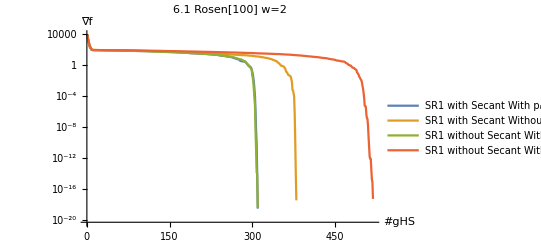

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
TrialTagList={
{"SR1 with Secant","With p_k"},
{"SR1 with Secant","Without p_k"},
{"SR1 without Secant","With p_k"},
{"SR1 without Secant","Without p_k"}};
STag="6.1";
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
w=2;
QNDataList=Table[
{HTag, ITag}=TrialTagList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TrialTagList]}];
LegendList=Table[
{HTag, ITag}=TrialTagList⟦i⟧;
StringJoin[HTag," ",  ITag],{i,Length[TrialTagList]}];
plotLabel=StringJoin[STag," Rosen[100] w=2"];
CompareObjectivePics[
LegendList,
plotLabel][QNDataList]
```

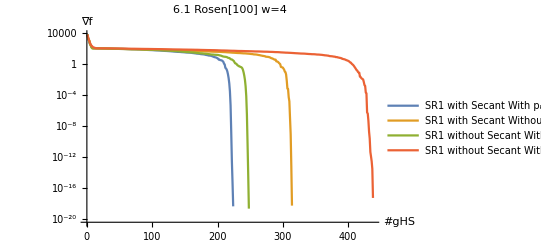

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
TrialTagList={
{"SR1 with Secant","With p_k"},
{"SR1 with Secant","Without p_k"},
{"SR1 without Secant","With p_k"},
{"SR1 without Secant","Without p_k"}};
STag="6.1";
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
w=4;
QNDataList=Table[
{HTag, ITag}=TrialTagList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TrialTagList]}];
LegendList=Table[
{HTag, ITag}=TrialTagList⟦i⟧;
StringJoin[HTag," ",  ITag],{i,Length[TrialTagList]}];
plotLabel=StringJoin[STag," Rosen[100] w=4"];
CompareObjectivePics[
LegendList,
plotLabel][QNDataList]
```

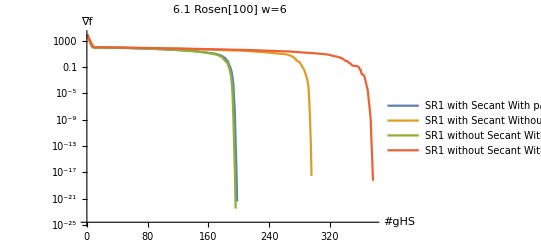

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
TrialTagList={
{"SR1 with Secant","With p_k"},
{"SR1 with Secant","Without p_k"},
{"SR1 without Secant","With p_k"},
{"SR1 without Secant","Without p_k"}};
STag="6.1";
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
w=6;
QNDataList=Table[
{HTag, ITag}=TrialTagList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TrialTagList]}];
LegendList=Table[
{HTag, ITag}=TrialTagList⟦i⟧;
StringJoin[HTag," ",  ITag],{i,Length[TrialTagList]}];
plotLabel=StringJoin[STag," Rosen[100] w=6"];
CompareObjectivePics[
LegendList,
plotLabel][QNDataList]
```

Conclusion, It is important to include the “secant” update either explicitly as a preliminary single vector update and/or by including the previous step in the sampled directions.

{{SR1 with Secant,With p_k},{SR1 without Secant,With p_k},{SR1 with Secant,Without p_k},{SR1 without Secant,Without p_k}}

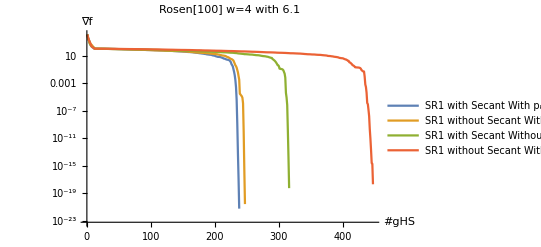

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
STag="6.1";
TagTriaList={
{"SR1 with Secant","With p_k"},
{"SR1 without Secant","With p_k"},
{"SR1 with Secant","Without p_k"},
{"SR1 without Secant","Without p_k"}}
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
w=4;
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
QNDataList=Table[
{HTag,ITag}=TagTriaList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TagTriaList]}];
CompareObjectivePics[
Table[
{HTag,ITag}=TagTriaList⟦i⟧;
StringJoin[HTag, " ", ITag],{i,Length[TagTriaList]}],
StringJoin["Rosen[100] w=4 with ", STag]][QNDataList]
```

## Comparing Sample Algorithms with w=4

I have three sample selection algorithms. 6.1 → 6.3.

There is something mysterious here.  With pk and without pk are different.

### Comparing SR1 on std Rosen with sample variants. “With pk”

6.3 is pretty consistently worst with 6.1 and 6.2 pretty close together.

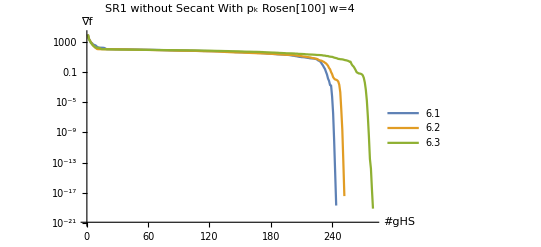

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{STag, ITag}={"SR1 with Secant","With p_k"};
TrialTagList={"6.1","6.2", "6.3"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
w=4;
QNDataList=Table[
STag=TrialTagList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TrialTagList]}];
LegendList=TrialTagList;
plotLabel=StringJoin[HTag," ", ITag," Rosen[100] w=4"];
CompareObjectivePics[
LegendList,
plotLabel][QNDataList]
```

### Comparing SR1 on std Rosen with sample variants. “Without pk” but with Secant

6.1 and 6.2 pretty close together 6.3 worst

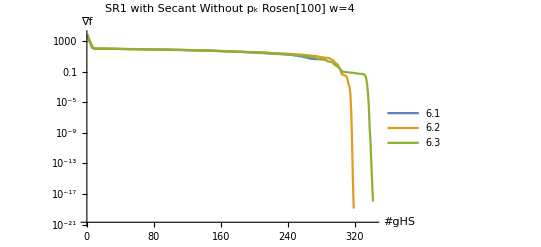

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{HTag, ITag}={"SR1 with Secant","Without p_k"};
TrialTagList={"6.1","6.2", "6.3"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
w=4;
QNDataList=Table[
STag=TrialTagList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TrialTagList]}];
LegendList=TrialTagList;
plotLabel=StringJoin[HTag," ", ITag," Rosen[100] w=4"];
CompareObjectivePics[
LegendList,
plotLabel][QNDataList]
```

### Comparing SR1 on std Rosen with sample variants. “Without pk” and without Secant

6.3 best with 6.1 and 6.2 pretty close together.

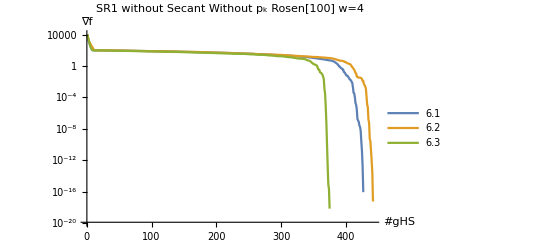

```mathematica
(* Set Dimensions and Safeguards *)
{n,w,δ,ΔMax}={100,1,1.0*10^-10,100};
{HTag, ITag}={"SR1 without Secant","Without p_k"};
TrialTagList={"6.1","6.2", "6.3"};
x0=RandomReal[{-1.2,1.2},n];
(* Testing on tstd Gen Rosenbrock a=100 NOT the Cuter version *)
a=100.0;f=Rosen[a];
(* Initializing State *)
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
(* Running MaxIter steps and storing all the output *)
{ϵ,MaxIter,hMin}={10^-7,10^3,10^-12};
Clear[QNDataList]
w=4;
QNDataList=Table[
STag=TrialTagList⟦i⟧;
QNState0=QNStateInitialize[f,HTag,ΔMax,δ,w][x0];
NestWhileList[QNUpdate[f,STag,HTag,ITag],QNState0,(And[Norm[#⟦3⟧]>ϵ, #⟦6⟧>hMin])&,1,MaxIter],
{i,Length[TrialTagList]}];
LegendList=TrialTagList;
plotLabel=StringJoin[HTag," ", ITag," Rosen[100] w=4"];
CompareObjectivePics[
LegendList,
plotLabel][QNDataList]
```